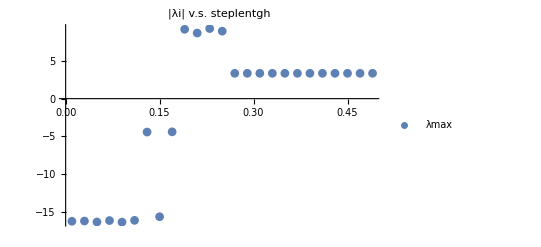

```mathematica
ListPlot[ang,PlotMarkers->Automatic,PlotLegends->{"λmax","λmin"}, PlotLabel->"|λi| v.s. steplentgh"]
```

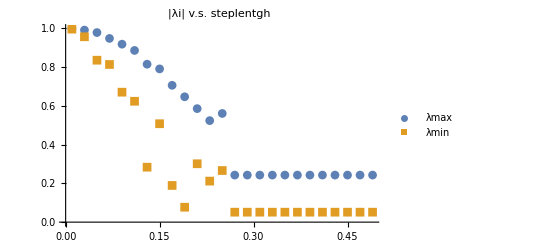

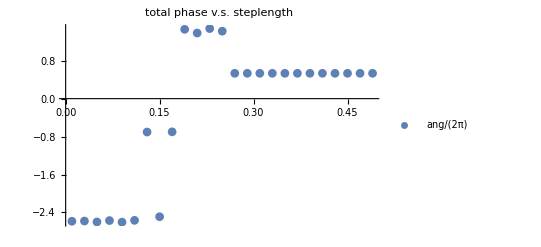

```mathematica
(*gs=0, *)
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/teststeplength","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
steplength=Table[codbar[[i]][[1]],{i,1,n}];
maxamp=Table[{steplength[[i]],codbar[[i]][[2]]},{i,1,n}];
minamp=Table[{steplength[[i]],codbar[[i]][[3]]},{i,1,n}];
ang=Table[{steplength[[i]],codbar[[i]][[4]]/(2π)},{i,1,n}];

ListPlot[{maxamp, minamp},PlotMarkers->Automatic,PlotLegends->{"λmax","λmin"}, PlotLabel->"|λi| v.s. steplentgh"]
ListPlot[ang,PlotMarkers->Automatic,PlotLegends->{"ang/(2π)"}, PlotLabel->"total phase v.s. steplength"]
(*ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
Sum[ang[[i]][[2]],{i,n}]
(10*3+1)*0.5*0.7/3//N*)
```

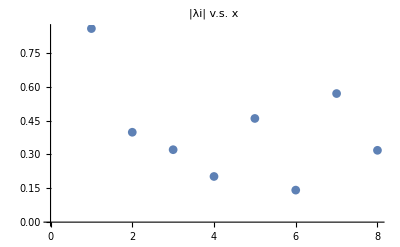

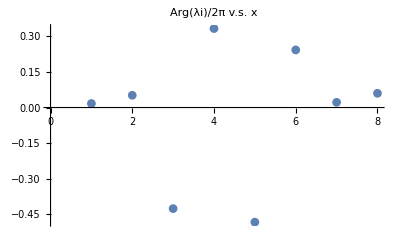

-0.183516

3.61667

```mathematica
(*gs=0, *)
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/teststeplength_0.2_0","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
Sum[ang[[i]][[2]],{i,n}]
(10*3+1)*0.5*0.7/3//N
```

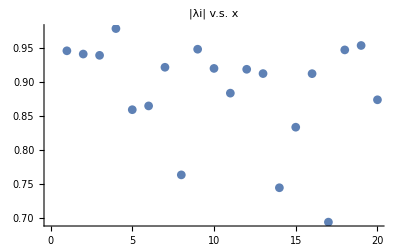

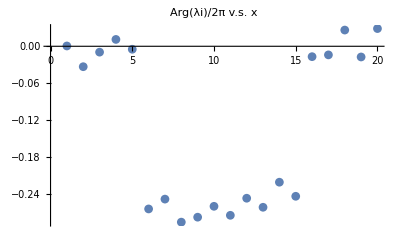

-2.60539

3.61667

```mathematica
(*gs=0, *)
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/teststeplength_0.1_0","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
Sum[ang[[i]][[2]],{i,n}]
(10*3+1)*0.5*0.7/3//N
```

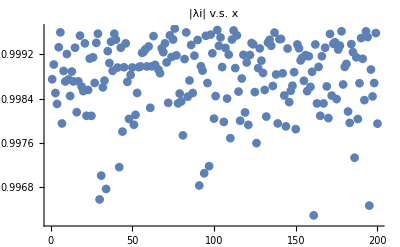

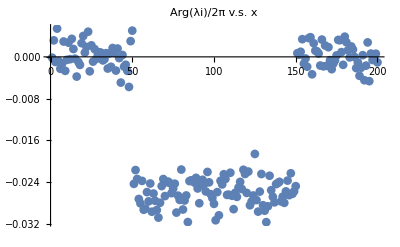

-2.57161

2.58333

```mathematica
(*gs=0, *)
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/teststeplength_0.01_0","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
Sum[ang[[i]][[2]],{i,n}]
(10*3+1)*0.5*0.5/3//N
Product[amp[[i]][[2]],{i,n}];
```

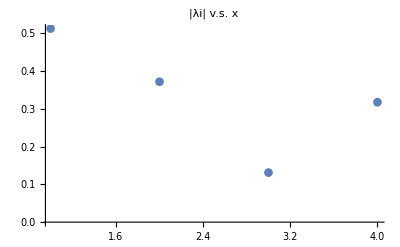

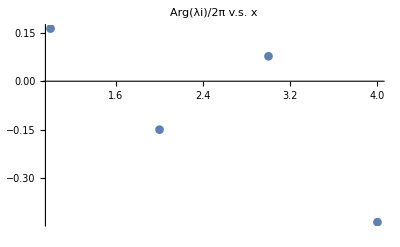

-0.345535

2.58333

0.00796502

```mathematica
(*gs=0, *)
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/teststeplength_0.5_0","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
Sum[ang[[i]][[2]],{i,n}]
(10*3+1)*0.5*0.5/3//N
Product[amp[[i]][[2]],{i,n}]
```

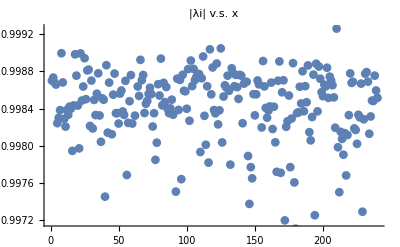

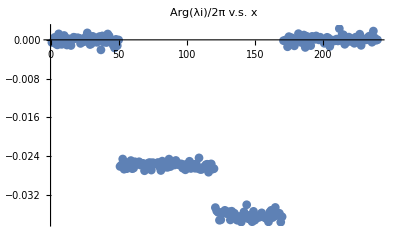

-3.62064

3.61667

0.678048

```mathematica
(*berry phase for 0.5*0.7 retangular loop.*)
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_stateretang","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
Sum[ang[[i]][[2]],{i,n}]
(10*3+1)*0.5*0.7/3//N
Product[amp[[i]][[2]],{i,n}]
```

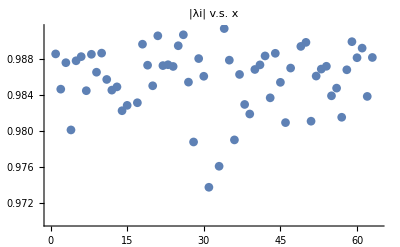

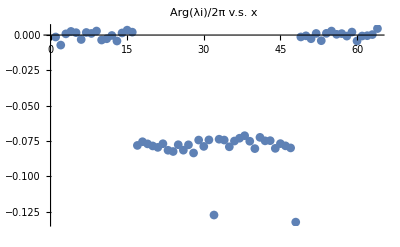

-2.58109

0.360824

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_statenew","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
Sum[ang[[i]][[2]],{i,n}]
Product[amp[[i]][[2]],{i,n}]
```

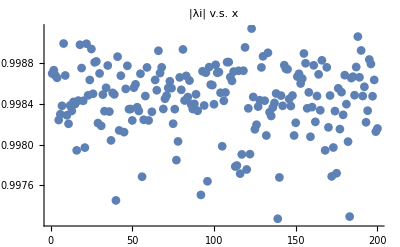

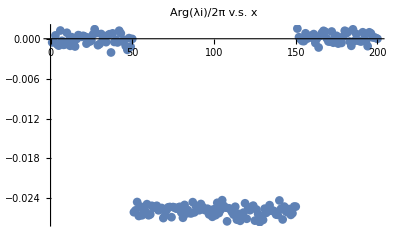

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_state","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
```

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_stateold","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
Sum[ang[[i]][[2]],{i,1,n}]
```

-Graphics-

-Graphics-

-2.58572

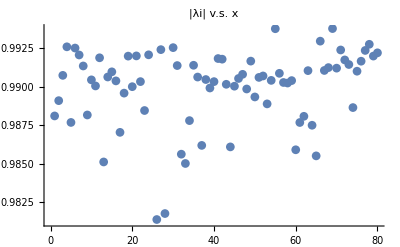

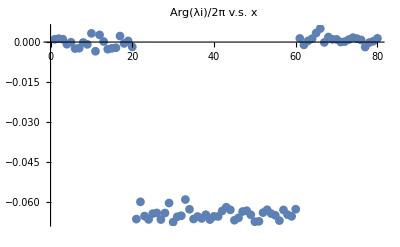

-2.57432

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_state00","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
Sum[ang[[i]][[2]],{i,1,n}]
```

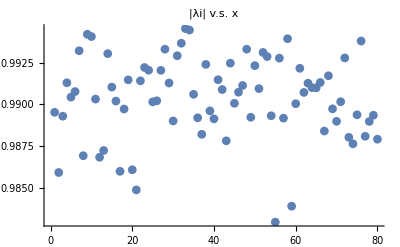

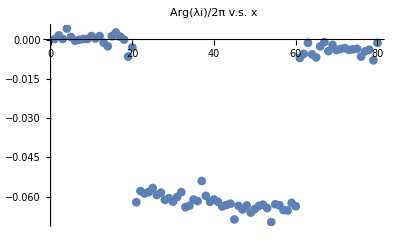

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_state11","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
```

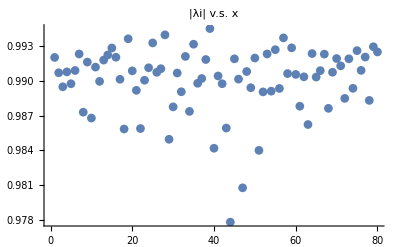

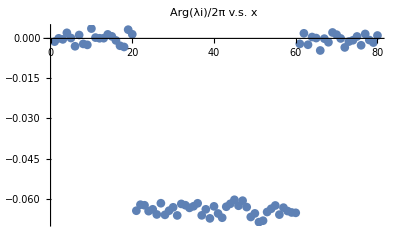

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_state0","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
```

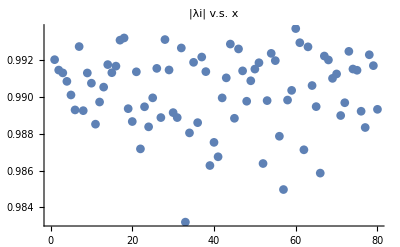

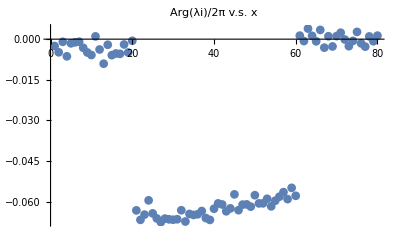

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_state1","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
```

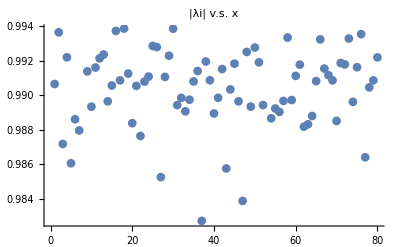

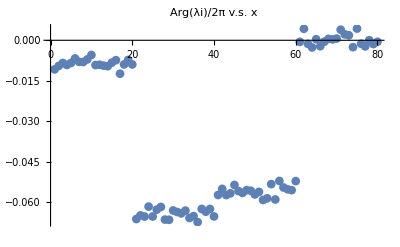

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/berryphase_singlestate/berry_laughlin_single_state2","Table"];
n:=Length[codbar]
d=Table[i,{i,1,n,1}];
amp=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
ang=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];

ListPlot[amp,PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[ang,PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
```